```mathematica
dataWeek3={{1,27},{2,43},{3,54},{4,64},{5,75},{6,82},{7,84},{8,89},{9,92},{10,93},{11,97},{12,104},{13,106},{14,111},{15,116},{16,122},{17,122},{18,127},{19,128},{20,129},{21,131},{22,132},{23,134},{24,135},{25,136}}
```

{{1,27},{2,43},{3,54},{4,64},{5,75},{6,82},{7,84},{8,89},{9,92},{10,93},{11,97},{12,104},{13,106},{14,111},{15,116},{16,122},{17,122},{18,127},{19,128},{20,129},{21,131},{22,132},{23,134},{24,135},{25,136}}

```mathematica
ShortGoel=a*(1-Exp[-b*t]);
GeneralGoel=a*(1-Exp[-b*t^c]);
delayedSshapedModel=a (1-(1+b*t) Exp[-b*t]);
shortGoel=NonlinearModelFit[dataWeek3,ShortGoel,{a,b},t]
```

FittedModel[135.974 (1-ⅇ^(-0.138257 t))]

```mathematica
shortGoel["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 135.974 | 3.00942 | 45.1829 | 5.72939×10^-24
b | 0.138257 | 0.00896322 | 15.425 | 1.27229×10^-13

```mathematica
shortGoel["BestFitParameters"]
```

{a→135.974,b→0.138257}

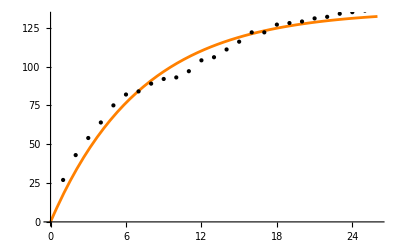

```mathematica
Plot[shortGoel[t],{t,0,26},Epilog->Point[dataWeek3],PlotStyle-> Orange]
```

```mathematica
generalGoel=NonlinearModelFit[dataWeek3,GeneralGoel,{{a,136},b,c},t]
```

FittedModel[190.443 (1-ⅇ^(-0.167696 t^(«18»)))]

```mathematica
generalGoel["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 190.443 | 19.068 | 9.98756 | 1.2348×10^-9
b | 0.167696 | 0.0124867 | 13.43 | 4.44399×10^-12
c | 0.633089 | 0.0410005 | 15.441 | 2.73814×10^-13

```mathematica
generalGoel["BestFitParameters"]
```

{a→190.443,b→0.167696,c→0.633089}

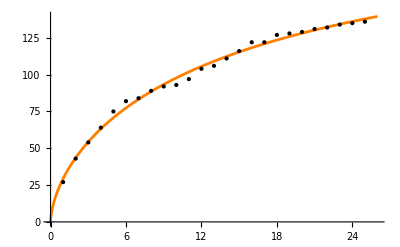

```mathematica
Plot[generalGoel[t],{t,0,26},Epilog->Point[dataWeek3],PlotStyle->Orange]
```

```mathematica
delayedSshaped=NonlinearModelFit[dataWeek3,delayedSshapedModel,{a,b},t]
```

FittedModel[124.672 (1-ⅇ^(-0.355907 t) (1+0.355907 t))]

```mathematica
delayedSshaped["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 124.672 | 3.52272 | 35.391 | 1.46032×10^-21
b | 0.355907 | 0.0292121 | 12.1835 | 1.63157×10^-11

```mathematica
delayedSshaped["BestFitParameters"]
```

{a→124.672,b→0.355907}

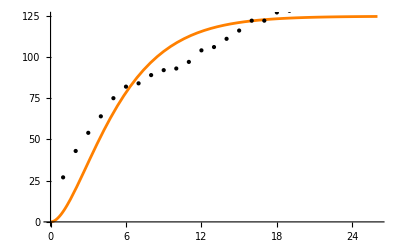

```mathematica
Plot[delayedSshaped[t],{t,0,26},Epilog->Point[dataWeek3],PlotStyle->Orange]
```

```mathematica
Gompertz=a*Exp[-α*Exp[-β*t]];
GompertzMakeham=a*(1-Exp[-λ*t-(α/β)*(Exp[β*t]-1)]);
gompertz=NonlinearModelFit[dataWeek3,Gompertz,{{a,136},{α,0.1},{β,0.1}},t]
```

FittedModel[140.65 ⅇ^(-1.50002 ⅇ^(«1»))]

```mathematica
gompertz["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 140.65 | 3.34768 | 42.0141 | 1.66356×10^-22
α | 1.50002 | 0.0733906 | 20.4388 | 8.46133×10^-16
β | 0.141582 | 0.0119094 | 11.8882 | 4.75715×10^-11

```mathematica
gompertz["BestFitParameters"]
```

{a→140.65,α→1.50002,β→0.141582}

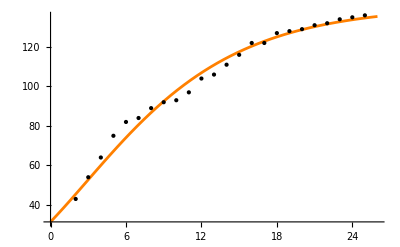

```mathematica
Plot[gompertz[t],{t,0,26},Epilog->Point[dataWeek3],PlotStyle->Orange]
```

```mathematica
gompertzMakeham=NonlinearModelFit[dataWeek3,GompertzMakeham,{{a,136},α,β,{λ,0.1}},t,PrecisionGoal->Infinity]
```

FittedModel[168.029 (1-ⅇ^(0.293737 «1»-«1»))]

```mathematica
gompertzMakeham["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 168.029 | 12.5901 | 13.3461 | 1.0007×10^-11
α | 0.148747 | 0.0227301 | 6.54404 | 1.75547×10^-6
β | -0.506395 | 0.142642 | -3.55011 | 0.00189446
λ | 0.0573606 | 0.0139226 | 4.11997 | 0.00048773

```mathematica
gompertzMakeham["BestFitParameters"]
```

{a→168.029,α→0.148747,β→-0.506395,λ→0.0573606}

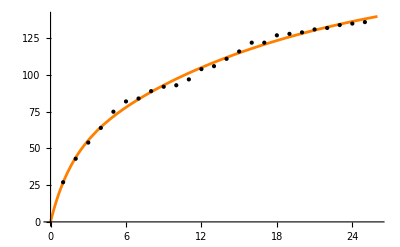

```mathematica
Plot[gompertzMakeham[t],{t,0,26},Epilog->Point[dataWeek3],PlotStyle->Orange]
```

```mathematica
modelPham=a*(1-(β/(β-1+a^{t^b}))^α);
pham=NonlinearModelFit[dataWeek3,modelPham,{{a,136},{b,0.1},{α,0.5},{β,0.75}},t]

Zhang=((1-(((1+α)*Exp[-b*t]))/(1+α*Exp[-b*t]))^{(c/b)*(p-β)})*(a/(p-β));

Chang=a*(1-(β/(β+(α*t)^b))^α);

YamadaExp=a*(1-Exp[-r*α*(1-Exp[-β*t])]);
```

FittedModel[368.987 (1-1.10791 (1/(«1»«1»«1»))^(«20»))]

```mathematica
pham["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 368.987 | 851.294 | 0.433443 | 0.669113
b | 0.365975 | 0.429657 | 0.851784 | 0.403943
α | 0.0298675 | 0.0426734 | 0.699909 | 0.491665
β | 30.9052 | 161.476 | 0.191392 | 0.850057

```mathematica
/**Pham не е подходящ модел за нашите данни/
```

```mathematica
zhang=NonlinearModelFit[dataWeek3,Zhang,{{α,-0.4},{b,0.1},{c,0.75},{p,0.5},{a,136},{β,-0.2}},t,MaxIterations->Infinity,PrecisionGoal->Infinity]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[213.449 (1-(«22» «1»)/(1«1»«19»«1»«1»))^0.59109]

```mathematica
zhang["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
α | -0.999176 | 3567.05 | -0.000280113 | 0.999779
b | 0.0000300406 | 130.09 | 2.30922×10^-7 | 1.
c | 0.0000927815 | 401.69 | 2.30978×10^-7 | 1.
p | 0.245691 | 100.882 | 0.00243543 | 0.998082
a | 40.8503 | 0.471715 | 86.5995 | 3.82187×10^-26
β | 0.0543089 | 100.882 | 0.000538341 | 0.999576

```mathematica
zhang["BestFitParameters"]
```

{α→-0.999176,b→0.0000300406,c→0.0000927815,p→0.245691,a→40.8503,β→0.0543089}

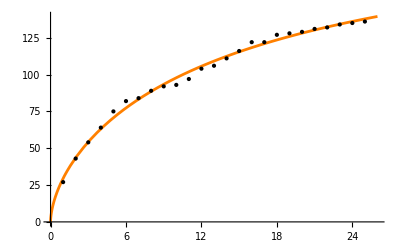

```mathematica
Plot[zhang[t],{t,0,26},Epilog->Point[dataWeek3],PlotStyle->Orange]
```

```mathematica
chang=NonlinearModelFit[dataWeek3,Chang,{{a,140},{b,5},{α,0.75},{β,0.3}},t,Method->"Newton"]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[554.937 (1-0.974445 (1/(«1»«1»«1»))^(«19»))]

```mathematica
chang["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 554.937 | 2869.6 | 0.193385 | 0.848516
b | 0.751364 | 0.292524 | 2.56855 | 0.0179053
α | 0.186267 | 1.48354 | 0.125556 | 0.901277
β | 0.870245 | 8.22609 | 0.105791 | 0.916752

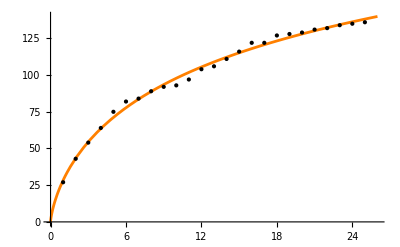

```mathematica
Plot[chang[t],{t,0,26},Epilog->Point[dataWeek3],PlotStyle->Orange]
```

```mathematica
yamada=NonlinearModelFit[dataWeek3,YamadaExp,{{a,140},{r,0.2},{α,0.4},{β,-0.3}},t]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[135.944 (1-ⅇ^(839.687 (1-«1»)))]

```mathematica
yamada["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 135.944 | 9.55951 | 14.2208 | 2.99602×10^-12
r | 20.4896 | 3797.94 | 0.00539494 | 0.995746
α | -40.9811 | 1898.88 | -0.0215817 | 0.982985
β | -0.0001645 | 0.0381094 | -0.00431653 | 0.996597

```mathematica
yamada["BestFitParameters"]
```

{a→135.944,r→20.4896,α→-40.9811,β→-0.0001645}

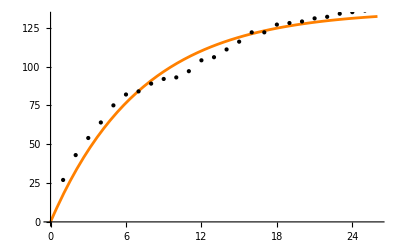

```mathematica
Plot[yamada[t],{t,0,26},Epilog->Point[dataWeek3],PlotStyle->Orange]
```

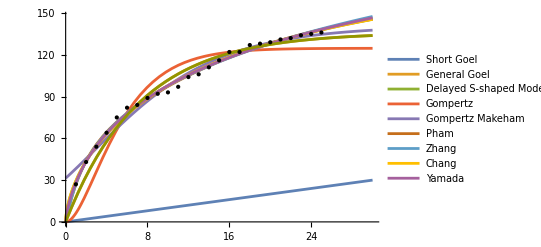

```mathematica
Plot[{t,shortGoel[t],generalGoel[t],delayedSshaped[t],gompertz[t],gompertzMakeham[t],pham[t],zhang[t],chang[t],yamada[t]},{t,0,30},Epilog->Point[dataWeek3],PlotStyle->{"Orange","purple","green","blue","red","pink","yellow","maroon","lime","olive"},PlotLegends->{"Short Goel","General Goel","Delayed S-shaped Model","Gompertz","Gompertz Makeham","Pham","Zhang","Chang","Yamada"}]
```

```mathematica
Grid[{#,shortGoel[#],generalGoel[#],delayedSshaped[#],gompertz[#],gompertzMakeham[#],pham[#],zhang[#],chang[#],yamada[#]}&[{"AIC","BIC","RSquared","AdjustedRSquared"}],Frame->All]
```

AIC | BIC | RSquared | AdjustedRSquared
162.592 | 166.249 | 0.997259 | 0.99702
123.546 | 128.422 | 0.999472 | 0.999399
197.436 | 201.093 | 0.988952 | 0.987991
148.691 | 153.566 | 0.998555 | 0.998358
120.739 | 126.833 | 0.999567 | 0.999484
123.822 | 129.916 | 0.99951 | 0.999417
130.639 | 139.171 | 0.999462 | 0.999293
124.831 | 130.925 | 0.99949 | 0.999393
166.908 | 173.002 | 0.997254 | 0.996731

```mathematica
prediction=Table[{i,Round[gompertzMakeham[i]]},{i,26,50}]
```

{{26,140},{27,141},{28,143},{29,144},{30,146},{31,147},{32,148},{33,149},{34,150},{35,151},{36,152},{37,153},{38,154},{39,155},{40,155},{41,156},{42,157},{43,157},{44,158},{45,159},{46,159},{47,160},{48,160},{49,160},{50,161}}

```mathematica
Show[Plot[gompertzMakeham[t],{t,0,51},Epilog->Point[dataWeek3]]&Plot[prediction[t],PlotStyle->Red]]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Show::gtype: Times is not a type of graphics.

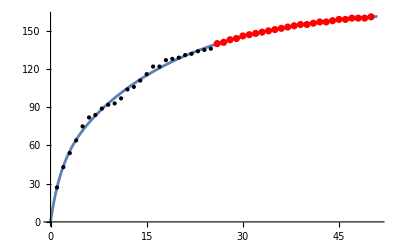

```mathematica
Show[Plot[gompertzMakeham[t],{t,0,51},Epilog->Point[dataWeek3]],ListPlot[prediction,PlotStyle->Red]]
```

```mathematica
dataSetSelf={{1,27},{2,43},{3,54},{4,64},{5,75},{6,82},{7,84},{8,89},{9,100},{10,103},{11,107},{12,109},{13,116},{14,121},{15,136},{16,142},{17,142},{18,147},{19,148},{20,149}}
```

{{1,27},{2,43},{3,54},{4,64},{5,75},{6,82},{7,84},{8,89},{9,100},{10,103},{11,107},{12,109},{13,116},{14,121},{15,136},{16,142},{17,142},{18,147},{19,148},{20,149}}

```mathematica
shortGoelSelf=NonlinearModelFit[dataSetSelf,ShortGoel,{a,b},t]
```

FittedModel[165.925 (1-ⅇ^(-0.106185 t))]

```mathematica
shortGoelSelf["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 165.925 | 8.23193 | 20.1562 | 8.42105×10^-14
b | 0.106185 | 0.0110922 | 9.57289 | 1.74086×10^-8

```mathematica
shortGoelSelf["BestFitParameters"]
```

{a→165.925,b→0.106185}

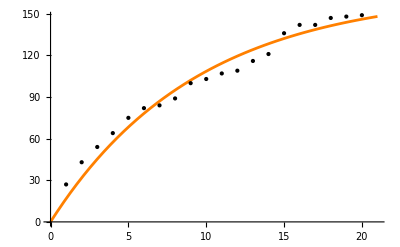

```mathematica
Plot[shortGoelSelf[t],{t,0,21},Epilog->Point[dataSetSelf],PlotStyle->Orange]
```

```mathematica
generalGoelSelf=NonlinearModelFit[dataSetSelf,GeneralGoel,{{a,150},{b,-0.5},{c,0.7}},t,MaxIterations->Infinity,PrecisionGoal->Infinity]
```

FittedModel[-871.227 (1-ⅇ^(0.0336035 t^(«19»)))]

```mathematica
generalGoelSelf["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | -871.227 | 2993.13 | -0.291076 | 0.774515
b | -0.0336035 | 0.11584 | -0.290086 | 0.775259
c | 0.525054 | 0.0906482 | 5.79221 | 0.0000216568

```mathematica
generalGoelSelf["BestFitParameters"]
```

{a→-871.227,b→-0.0336035,c→0.525054}

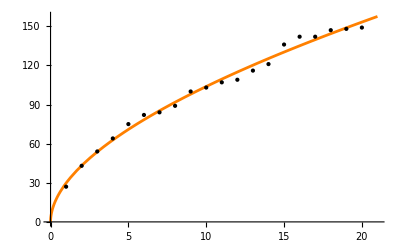

```mathematica
Plot[generalGoelSelf[t],{t,0,21},Epilog->Point[dataSetSelf],PlotStyle->Orange]
```

```mathematica
delayedSshapedSelf=NonlinearModelFit[dataSetSelf,delayedSshapedModel,{a,b},t]
```

FittedModel[139.253 (1-ⅇ^(-0.315791 t) (1+0.315791 t))]

```mathematica
delayedSshapedSelf["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 139.253 | 6.09159 | 22.8599 | 9.47619×10^-15
b | 0.315791 | 0.0309478 | 10.204 | 6.53948×10^-9

```mathematica
delayedSshapedSelf["BestFitParameters"]
```

{a→139.253,b→0.315791}

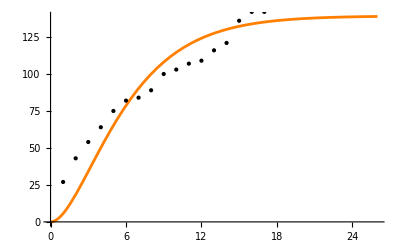

```mathematica
Plot[delayedSshapedSelf[t],{t,0,26},Epilog->Point[dataSetSelf],PlotStyle->Orange]
```